```mathematica
ClearAll["Global`*"]
$Assumptions=A∈Integers&&A>2&&α∈Reals&&α>0&&λ∈Reals&&λ>=0&&β∈Reals&&β>0&&R∈Reals&&Rp∈Reals&&a∈Reals&&a>0&&lam∈Reals&&lam>0;
verbosity=1;
```

```mathematica
spacedim=3;
A=4;
F=2;
Z={A/2,A/2};
If[Total[Z]!=A||Dimensions[Z][[1]]!=F,Print["System definition erroneous."]]
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1]... Subscript[B, Subscript[Z, 1]]... Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
idPairs=Table[{n,n+Z[[1]]},{n,Z[[1]]}];
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1] Subscript[B, 2].Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
(*idPairs={{1,Z[[1]]+1}}*)

FrgExpWidthsR=Array[Subscript["α^r", ##]&,{F}];
FrgExpWidthsL=Array[Subscript["α^l", ##]&,{F}];

intPairs=Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}];
intBosePairs=Complement[intPairs,idPairs];
intTriples=Union[Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[2]]≠#[[3]]&],Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[1]]≠#[[2]]&]];
intBoseTriples={};
Do[
addtriple=True;
Do[
If[SubsetQ[tri,pai],addtriple=False,0]
,{pai,idPairs}];
If[addtriple,AppendTo[intBoseTriples,tri]];
,{tri,intTriples}];
intBoseTriples=DeleteDuplicates[Table[Sort[intBoseTriples[[n]]],{n,Length[intBoseTriples]}]];
intPart=Join[Table[AppendTo[intBosePairs[[n]],intBosePairs[[n]][[1]]],{n,Length[intBosePairs]}],intBoseTriples,{{1,1,1}}];

If[verbosity>0,
Print["F_1 ⊕ F_2 = "<>ToString[Z[[1]]]<>" ⊕ "<>ToString[Z[[2]]]]
Print["Inter-cluster interaction:\n","∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = "<>ToString[Length[intBosePairs]]<>"·δ_ij + "<>ToString[Length[intBoseTriples]]<>"·δ_ijδ_ik"]
Print["Pairs = ",intBosePairs,"   Triples = ",intBoseTriples]
]
```

F_1 ⊕ F_2 = 2 ⊕ 2

Inter-cluster interaction:
∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = 2·δ_ij + 0·δ_ijδ_ik

Pairs = {{1,4,1},{2,3,2}}   Triples = {}

Null^3

```mathematica
SingleToCluster={};
For[f=1,f≤F,f++,{
For[i=1,i≤Z[[f]]-1,i++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+1]],0,j==Prepend[Accumulate[Z],0][[f]]+i,(Z[[f]]-1)/Z[[f]],1==1,-1/Z[[f]]],{j,1,A}]
]
}];
}];
For[f=1,f<F,f++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+2]],0,j<=Prepend[Accumulate[Z],0][[f+1]],1/Z[[f]],1==1,-1/Z[[f+1]]],{j,1,A}]
]
}];
AppendTo[SingleToCluster,
Table[1/A,{j,1,A}]
];
Single=Array[Subscript["r⃗", ##]&,{A}];
Cluster=Flatten[Table[Array[Subscript["r̄", Prepend[Accumulate[Z],0][[f]]+##]&,{Z[[f]]-1}],{f,F}]];
AppendTo[Cluster,ArrayFlatten[Array[Subscript["R⃗", ##]&,{F-1}],1][[1]]];AppendTo[Cluster,"(R⃗)_cm"];
Tmat=SingleToCluster;
Tmatinv=Inverse[SingleToCluster];
TproR=Table[If[(m==A-1),Tmat[[m,n]],0],{m,A},{n,A}];
If[verbosity>0,
Print[Cluster//MatrixForm,"=",SingleToCluster//MatrixForm,"·",Single//MatrixForm]
Print[Cluster//MatrixForm,"=",TproR//MatrixForm,"·",Single//MatrixForm]]
```

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(1/2 | -1/2 | 0 | 0
0 | 0 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2
1/4 | 1/4 | 1/4 | 1/4)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 0)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

Null^2

```mathematica
Wmat={};
posInW=0;
For[f=1,f≤F,f++,(
If[Z[[f]]>1,
posInW+=1;
AppendTo[Wmat,Table[If[pos==posInW,Table[If[m==n,4 FrgExpWidthsR[[pos]],2 FrgExpWidthsR[[pos]]],{n,Z[[f]]-1},{m,Z[[f]]-1}],0],{pos,F}]];
];
)];
Wmat=Table[If[(m>A-2)||(n>A-2),0,ArrayFlatten[Wmat][[n]][[m]]],{n,A},{m,A}];
If[verbosity>0,Print[Wmat//MatrixForm]]
```

(4 (α^r)_1 | 0 | 0 | 0
0 | 4 (α^r)_2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Pij[i_,j_]:=Table[If[((r==i)&&(c==j))||((r==j)&&(c==i))||((r≠i)&&(c≠j)&&(c==r)),1,0],{r,1,A},{c,1,A}];

Perm[ord_]:=
Module[{},
pmat=IdentityMatrix[A];
Do[
pmat[[move[[1]],move[[1]]]]=0;
pmat[[move[[2]],move[[1]]]]=1;
,{move,ord}];
If[(Total[pmat,{1}]==ConstantArray[1,A])&&(Total[pmat,{2}]==ConstantArray[1,A]),
pmat,Print["illdefined permutation!"]]
];

interFragmentAntisymmetrizer=Flatten[Table[Join[DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],
Map[Reverse,DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],2],2
],{n,0,Length[idPairs]}],1];
If[verbosity>0,Print["Inter-cluster anti-symmetrizer:\n (Â)_AB = ",interFragmentAntisymmetrizer];]
```

Inter-cluster anti-symmetrizer:
 (Â)_AB = {{},{{1,3},{3,1}},{{2,4},{4,2}},{{1,3},{2,4},{4,2},{3,1}}}

```mathematica
Pv[i_,j_]:=Table[If[(n==m==j)||(n==m==i),1,0],{n,A},{m,A}];
Vr[i_,j_,λ_]:=If[i≠j,Table[Which[((n==m==i))||((n==m==(j))),2 λ,((n==i)&&(m==j))||((m==i)&&(n==j)),-2 λ,1==1,0],{n,A},{m,A}],Table[0,{n,A},{m,A}]];
Vij[i_,j_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv;
Vijk[i_,j_,k_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv+Transpose[Pv[i,k].Tmatinv].Vr[i,k,λ].Pv[i,k].Tmatinv;
```

```mathematica
{ivtest,jvtest,kvtest}=intPart[[-1]];
testperm={};(*{{1,4},{4,1},{2,5},{5,2},{3,6},{6,3}}*)
λ=0;
Wfull[iv_,jv_,kv_,permu_,λ_]:=Flatten[Wmat/.{FrgExpWidthsR[[#]]->FrgExpWidthsL[[#]]&/@Range[F]},1]+Vijk[iv,jv,kv,λ]+Transpose[(Tmat.Perm[permu].Tmatinv)].(Wmat).(Tmat.Perm[permu].Tmatinv);
Sfull[permu_]:=TproR.Perm[permu].Tmatinv;
Amat[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[1;;(A-2),1;;(A-2)]];
S3[Rp_,s_,iv_,jv_,kv_,permu_,λ_]:=-Rp Wfull[iv,jv,kv,permu,λ][[A-1,1;;A-2]]-I s Sfull[permu][[A-1,1;;A-2]];
S4[s_,permu_]:=-I s Sfull[permu][[A-1,A-1]];
M1[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[A-1,A-1]];
If[verbosity>0,Print["W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = ",Wfull[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (S̲)_full = T_RPT^-1 = ",Sfull[testperm]//MatrixForm,"         (V̲)_ij = ",Vij[ivtest,jvtest,λ]//MatrixForm,"         (V̲)_ijk = ",Vijk[ivtest,jvtest,kvtest,λ]//MatrixForm]
Print["         A̲ = ",Amat[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (A̲)^-1 = ",Simplify[Inverse[Amat[ivtest,jvtest,kvtest,testperm,λ]]]//MatrixForm,"         S_3 = ",S3[Rp,s,ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         S_4 = ",S4[s,testperm]//MatrixForm,"         M_1 = ",M1[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm]]
```

W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = (4 (α^l)_1+4 (α^r)_1 | 0 | 0 | 0
0 | 4 (α^l)_2+4 (α^r)_2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)         (S̲)_full = T_RPT^-1 = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)         (V̲)_ij = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)         (V̲)_ijk = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

A̲ = (4 (α^l)_1+4 (α^r)_1 | 0
0 | 4 (α^l)_2+4 (α^r)_2)         (A̲)^-1 = (1/(4 (α^l)_1+4 (α^r)_1) | 0
0 | 1/(4 (α^l)_2+4 (α^r)_2))         S_3 = (0
0)         S_4 = -ⅈ s         M_1 = 0

Null^2

```mathematica
scoeff[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=CoefficientList[Simplify[1/2 S3[Rp,s,iv,jv,kv,permu,λ].Inverse[Amat[iv,jv,kv,permu,λ]].S3[Rp,s,iv,jv,kv,permu,λ]-1/2 Rp M1[iv,jv,kv,permu,λ] Rp+S4[s,permu] Rp+I s Rpp],s];
S5[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[2]]];
S6[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[1]]];
Kmat[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=
If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
-2 Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[3]]]
];
Kmatinv[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
1/Kmat[Rp,Rpp,iv,jv,kv,permu,λ]
];
If[verbosity>0,Print[S6[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ]," + ",S5[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s  +",Kmat[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s^2"]]
```

0 + -ⅈ (Rp-Rpp)s  +0s^2

```mathematica
genericRGMEQcomponent[R_,Rp_,a1_,a2_,lec_,lam_,ii_,jj_,kk_,permu_]:=Module[{λ},
kin=(lam==0);

Rcoeff=CoefficientList[
1/2 S5[R,Rp,ii,jj,kk,permu,lam] Kmatinv[R,Rp,ii,jj,kk,permu,lam] S5[R,Rp,ii,jj,kk,permu,lam]+S6[R,Rp,ii,jj,kk,permu,lam]
,Rp];

If[Length[Rcoeff]==0,αRp=αRRp=αR=0,αR=Simplify[Rcoeff[[1]]/.{α->a1,β->a2}]];
If[Length[Rcoeff]>1,αRRp=Simplify[Rcoeff[[2]]/.{α->a1,β->a2}],αRRp=0];
If[Length[Rcoeff]==3,αRp=Simplify[Rcoeff[[3]]/.{α->a1,β->a2}],αRp=0];

detA=Simplify[Det[Amat[ii,jj,kk,permu,lam]]/.{α->a1,β->a2}];
detK=If[Length[scoeff[R,Rp,ii,jj,kk,permu,lam]]<3,1,Simplify[Kmat[R,Rp,ii,jj,kk,permu,lam]/.{α->a1,β->a2}]];

strength=lec (Simplify[1/(2 Pi) (2 Pi)^((A-2)/2)/Sqrt[detA] (2 Pi)^(1/2)/Sqrt[detK]])^spacedim;

Simplify[strength Exp[Simplify[αR+αRp Rp^2+αRRp Rp]]]
];
```

```mathematica
a=α;b=β;
LEC=1;
lamba=0;
ivtest=2;jvtest=4;kvtest=2;
normierung1=genericRGMEQcomponent["r","r̃",a,b,LEC,lamba,ivtest,jvtest,kvtest,{}];
normierung =normierung1(2 Pi)^1.5;
If[verbosity>0,Print["Norm = ∫ϕ_Aϕ_B = ",normierung]]
```

Norm = ∫ϕ_Aϕ_B = 3.87578/((((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))^(3/2))

```mathematica
SetSharedVariable[RGMequationComponents]
RGMequationComponents={};
Clear[i]
ParallelDo[
WWcoef={"D_1","C_0","(T̂-E)"}[[Max[Counts[ijk]]]];
WWrange={Λ,Λ,0}[[Max[Counts[ijk]]]];
Do[
signpermut=(-1)^(Length[permu]/2);
AppendTo[RGMequationComponents,Simplify[signpermut genericRGMEQcomponent[x,y,α,β,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]]];
,{permu,interFragmentAntisymmetrizer}]e
,{ijk,intPart}]
```

```mathematica
TableForm[(*1/(normierung)*)Simplify[Total[RGMequationComponents]],TableSpacing->{5,5}]
```

((T̂-E) π^(3/2))/(16 √2 (((α^l)_2+(α^r)_1) ((α^l)_1+(α^r)_2))^(3/2))+((T̂-E) π^(3/2))/(16 √2 (((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))^(3/2))-((T̂-E) ⅇ^(-(4 x^2 (α^r)_1 (α^r)_2+(α^l)_2 ((x+y)^2 (α^r)_1+(x-y)^2 (α^r)_2)+(α^l)_1 (4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+(x+y)^2 (α^r)_2))/(2 ((α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(√2 (((α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 ((α^r)_1+(α^r)_2)+(α^l)_1 (4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 ((α^r)_1+(α^r)_2)+(α^l)_1 (4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))-(C_0 ⅇ^(-(4 x^2 (2 Λ+(α^r)_1) (α^r)_2+(α^l)_2 (2 (x+y)^2 Λ+(x+y)^2 (α^r)_1+(x-y)^2 (α^r)_2)+(α^l)_1 (2 x^2 Λ-4 x y Λ+2 y^2 Λ+4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+x^2 (α^r)_2+2 x y (α^r)_2+y^2 (α^r)_2))/(2 (2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(√2 ((2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))-(C_0 ⅇ^(-(4 x^2 (α^r)_1 (2 Λ+(α^r)_2)+(α^l)_2 ((x+y)^2 (α^r)_1+(x-y)^2 (2 Λ+(α^r)_2))+(α^l)_1 (4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+(x+y)^2 (2 Λ+(α^r)_2)))/(2 (2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(√2 ((2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))+(C_0 ⅇ^(-(2 x^2 Λ ((α^l)_2+(α^r)_1) ((α^l)_1+(α^r)_2))/(Λ (α^r)_1+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_2 (Λ+2 (α^r)_2))) π^(3/2))/(4 (Λ (α^r)_1+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_2 (Λ+2 (α^r)_2))^(3/2))+(C_0 ⅇ^(-(2 x^2 Λ ((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))/(Λ (α^r)_1+(α^l)_2 (Λ+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_2))) π^(3/2))/(4 (Λ (α^r)_1+(α^l)_2 (Λ+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_2))^(3/2))

```mathematica
Simplify[Total[RGMequationComponents(*/((2 π)^((NinF-1)/2)/(√((NinF) 2^(NinF-1) α^(NinF-1))))^(3 2)*)]/.{Subscript["\!\(\*SuperscriptBox[\(α\), \(r\)]\)", 1]->"α",Subscript["\!\(\*SuperscriptBox[\(α\), \(r\)]\)", 2]->"α",Subscript["\!\(\*SuperscriptBox[\(α\), \(l\)]\)", 1]->"α",Subscript["\!\(\*SuperscriptBox[\(α\), \(l\)]\)", 2]->"α",NinF->A/2}]
```

1/128 π^(3/2) (-(√2 (T̂-E) ⅇ^(-α (x^2+y^2)) (8/(1/α)^(3/2)-ⅇ^(α (x^2+y^2))))/((α^2)^(3/2))+(8 C_0 ((ⅇ^(-(2 α x^2 Λ)/(2 α+Λ)))/α^2-8 √(1/α) ⅇ^(-(α (2 α (x^2+y^2)+(3 x^2+y^2) Λ))/(2 α+Λ))) √(α (2 α+Λ)))/(2 α+Λ)^2)

the factor which multiplies (T-E) is equal to the integral over a product of 4 Gaussians with, in general, different width parameters corresponding to individual terms in the multi-Gauss expansion of the fragment wave functions.
⇓

```mathematica
normierung1
```

π^(3/2)/(16 √2 (((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))^(3/2))

compared with the analytic formula, the above includes a not-understood factor of 2·(2π)^(-3/2)

### A/2 different fermion species (ab)(ab), (abc)(abc), (abcd)(abcd), ...

2-2

(α^3 (-(√2 (T̂-E) ⅇ^(-α (x^2+y^2)) (8/(1/α)^(3/2)-ⅇ^(α (x^2+y^2))))/((α^2)^(3/2))+(8 C_0 ((ⅇ^(-(2 α x^2 Λ)/(2 α+Λ)))/α^2-8 √(1/α) ⅇ^(-(α (2 α (x^2+y^2)+(3 x^2+y^2) Λ))/(2 α+Λ))) √(α (2 α+Λ)))/(2 α+Λ)^2))/(16 π^(3/2))

3-3

4-4

5-5

6-6

this leads to the following analytic dependencies of the strengths and Gaussian fall-off widths, i.e., interaction ranges:

```mathematica
cRange[a_,l_,A_]:=A a l/(A a+(A-1) l)
cLEC[bareLEC_,a_,l_,A_]:=bareLEC A^2 (A a/(A a+(A-1) l))^(3/2)
d1Range[a_,l_,A_]:=4 A a l/(2 A a+(3 A-4) l)
d1LEC[bareLEC_,a_,l_,A_]:=bareLEC A (A (A-1))/2 (4 A a/(4 A a+8 (A-1) l+(3 A-4) l^2/a))^(3/2)
d2Range[a_,l_,A_]:=4 A a l (a+l)/(4 A a^2+8 (A-1/2) a l+(3 A-4) l^2)
d2LEC[bareLEC_,a_,l_,A_]:=bareLEC A (A (A-1))/2 (4 A a/(4 A a+8 (A-1/2) l+(3 A-4) l^2/a))^(3/2)
```

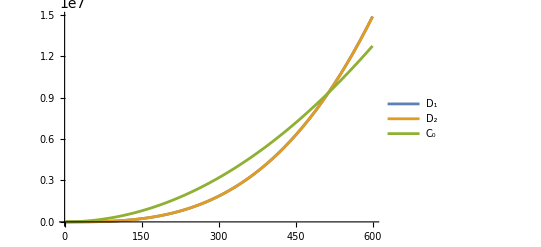

```mathematica
Plot[{d1LEC[1,1,1,aa],d2LEC[1,1,1,aa],cLEC[100,1,1,aa]},{aa,2,600},PlotLegends->{"D_1","D_2","C_0"}]
```

```mathematica
ParticlesInFragment=4;
λ=4;
α=1;
clec=-471.537;
dlec=-13.2493;
Animate[
Grid[{{
Plot[cLEC[clec,α,λ,ParticlesInFragment] Exp[-cRange[α,λ,ParticlesInFragment] r^2],{r,0,3},PlotLegends->{"2-body"},ImageSize->Large],Plot[{d1LEC[dlec,α,λ,ParticlesInFragment] Exp[-d1Range[α,λ,ParticlesInFragment] r^2],d2LEC[dlec,α,λ,ParticlesInFragment] Exp[-d2Range[α,λ,ParticlesInFragment] r^2]},{r,0,3},PlotLegends->{"3_1-body","3_2-body"},ImageSize->Large]}}]
,{ParticlesInFragment,2,630},AnimationRunning->False]
```

### All distinguishable (ab)(cd), (abc)(def), (abcd)(efgh), ...

2-2 (distinguishable, single-Gaussian approximation)

(√2 (T̂-E) α+(16 C_0 ⅇ^(-(2 x^2 α Λ)/(2 α+Λ)) α^(5/2))/(2 α+Λ)^(3/2)+16 √2 D_1 α^4 ((ⅇ^(-(4 x^2 α Λ)/(2 α+Λ)) √((2 α+Λ)^2))/(2 α+Λ)^4+(ⅇ^(-(4 x^2 α Λ (α+Λ))/(4 α^2+6 α Λ+Λ^2)))/((4 α^2+6 α Λ+Λ^2)^(3/2))))/(32 π^(3/2) α)

3-3 (distinguishable, single-Gaussian approximation)

((T̂-E)+27 √3 α^(3/2) ((C_0 ⅇ^(-(3 x^2 α Λ)/(3 α+2 Λ)))/(3 α+2 Λ)^(3/2)+(8 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+5 Λ)))/((12 α+16 Λ+(5 Λ^2)/α)^(3/2))+(8 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+20 α Λ+5 Λ^2)))/((12 α+20 Λ+(5 Λ^2)/α)^(3/2))))/(128 √2 π^(3/2))

4-4 (distinguishable, single-Gaussian approximation)

(√2 (T̂-E) α^3+(128 √2 C_0 ⅇ^(-(4 x^2 α Λ)/(4 α+3 Λ)) α^(9/2))/(4 α+3 Λ)^(3/2)+96 D_1 α^6 ((ⅇ^(-(2 x^2 α Λ)/(α+Λ)))/((2 α^2+3 α Λ+Λ^2)^(3/2))+(2 √2 ⅇ^(-(4 x^2 α Λ (α+Λ))/(4 α^2+7 α Λ+2 Λ^2)))/((4 α^2+7 α Λ+2 Λ^2)^(3/2))))/(2048 π^(3/2) α^3)

5-5 (distinguishable, single-Gaussian approximation)

((T̂-E)+125 √5 α^(3/2) ((C_0 ⅇ^(-(5 x^2 α Λ)/(5 α+4 Λ)))/(5 α+4 Λ)^(3/2)+(16 D_1 ⅇ^(-(20 x^2 α Λ)/(10 α+11 Λ)))/((20 α+32 Λ+(11 Λ^2)/α)^(3/2))+(16 D_1 ⅇ^(-(20 x^2 α Λ (α+Λ))/(20 α^2+36 α Λ+11 Λ^2)))/((20 α+36 Λ+(11 Λ^2)/α)^(3/2))))/(8192 √2 π^(3/2))

6-6 (distinguishable, single-Gaussian approximation, >e13mins on 8 kernels)

(√2 (T̂-E) α^5+432 √3 α^(13/2) ((C_0 ⅇ^(-(6 x^2 α Λ)/(6 α+5 Λ)))/(6 α+5 Λ)^(3/2)+(5 √2 D_1 ⅇ^(-(12 x^2 α Λ)/(6 α+7 Λ)))/((12 α+20 Λ+(7 Λ^2)/α)^(3/2))+(5 √2 D_1 ⅇ^(-(12 x^2 α Λ (α+Λ))/(12 α^2+22 α Λ+7 Λ^2)))/((12 α+22 Λ+(7 Λ^2)/α)^(3/2))))/(131072 π^(3/2) α^5)

7-7 (distinguishable, single-Gaussian approximation)

8-8 (distinguishable, single-Gaussian approximation)

9-9 (distinguishable, single-Gaussian approximation)

10-10 (distinguishable, single-Gaussian approximation)

this leads to the following analytic dependencies of the strengths and Gaussian fall-off widths, i.e., interaction ranges:

```mathematica
cRange[a_,l_,A_]:=A a l/(A a+(A-1) l)
cLEC[bareLEC_,a_,l_,A_]:=bareLEC A^2 (A a/(A a+(A-1) l))^(3/2)
d1Range[a_,l_,A_]:=4 A a l/(2 A a+(3 A-4) l)
d1LEC[bareLEC_,a_,l_,A_]:=bareLEC A (A (A-1))/2 (4 A a/(4 A a+8 (A-1) l+(3 A-4) l^2/a))^(3/2)
d2Range[a_,l_,A_]:=4 A a l (a+l)/(4 A a^2+8 (A-1/2) a l+(3 A-4) l^2)
d2LEC[bareLEC_,a_,l_,A_]:=bareLEC A (A (A-1))/2 (4 A a/(4 A a+8 (A-1/2) l+(3 A-4) l^2/a))^(3/2)
```

```mathematica
Plot[{d1LEC[1,1,1,aa],d2LEC[1,1,1,aa],cLEC[100,1,1,aa]},{aa,2,600},PlotLegends->{"D_1","D_2","C_0"}]
```

-Graphics-

```mathematica
ParticlesInFragment=4;
λ=4;
α=1;
clec=-471.537;
dlec=-13.2493;
Animate[
Grid[{{
Plot[cLEC[clec,α,λ,ParticlesInFragment] Exp[-cRange[α,λ,ParticlesInFragment] r^2],{r,0,3},PlotLegends->{"2-body"},ImageSize->Large],Plot[{d1LEC[dlec,α,λ,ParticlesInFragment] Exp[-d1Range[α,λ,ParticlesInFragment] r^2],d2LEC[dlec,α,λ,ParticlesInFragment] Exp[-d2Range[α,λ,ParticlesInFragment] r^2]},{r,0,3},PlotLegends->{"3_1-body","3_2-body"},ImageSize->Large]}}]
,{ParticlesInFragment,2,630},AnimationRunning->False]
```